# Sección de Poincaré

## Ecuaciones de Lorenz

Empezaremos ilustrando el concepto de la sección de Poincaré usando las ecuaciones de Lorenz:



En la gráfica siguiente observamos una trayectoria del sistema atravesando la sección de Poincaré definida, en este caso, como el cuarto de plano , , :

```mathematica
r=28;
s=10;
b=8/3;
```

```mathematica
slor=NDSolve[{x'[t]==s*(y[t]-x[t]),y'[t]==x[t]*(r-z[t])-y[t],z'[t]==x[t]*y[t]-b*z[t],x[0]==0,y[0]==1/100,z[0]==0},{x,y,z},{t,0,1000}];
```

```mathematica
pplt=ParametricPlot3D[Evaluate[{x[t],y[t],z[t]}/.slor],{t,0,100},MaxRecursion->10,ColorFunction->Function[{x,y,z,t},ColorData["TemperatureMap"][t]],AxesLabel->{x,y,z}];
```

```mathematica
zsurf=Plot3D[30,{x,0,30},{y,0,30}];
```

```mathematica
Show[pplt,zsurf]
```

-Graphics3D-

Aquí observamos como un ciclo límite atraviesa a la sección en un solo punto. Es decir, ciclos límites corresponden a puntos de equilibrio en el mapeo de Poincaré:

```mathematica
Show[ParametricPlot3D[{1,Cos[t],Sin[t]},{t,0,2*Pi},PlotStyle->Red,AxesLabel->{x,y,z}],Plot3D[0,{x,0,2},{y,0,2},AxesLabel->{x,y,z}]]
```

-Graphics3D-

En esta siguiente gráfica vemos las intersecciones de la trayectoria de las ecuaciones de Lorenz en la sección de Poincaré definida anteriormente. Los puntos están coloreados de azul a rojo mientras el tiempo va avanzando. Vemos que los puntos se van alejando aproximadamente de la coordenada , por lo que podríamos suponer que aproximadamente en ese punto existe un repulsor. En este caso, ese repulsor es uno de los puntos de equilibrio que surgen en la bifurcación de tridente supercrítica y que pierden estabilidad en la bifurcación de Hopf subcrítica.

```mathematica
data1=Reap[NDSolve[{x'[t]==s*(y[t]-x[t]),y'[t]==x[t]*(r-z[t])-y[t],z'[t]==x[t]*y[t]-b*z[t],x[0]==0,y[0]==1/100,z[0]==0,WhenEvent[z[t]==30&&x[t]≥0&&y[t]≥0,Sow[{x[t],y[t]}]]},{x,y},{t,0,1000},MaxSteps->∞]][[-1,1]];
```

```mathematica
Dimensions[data1]
```

{888,2}

```mathematica
data2=Reap[NDSolve[{x'[t]==s*(y[t]-x[t]),y'[t]==x[t]*(r-z[t])-y[t],z'[t]==x[t]*y[t]-b*z[t],x[0]==0,y[0]==2/100,z[0]==0,WhenEvent[z[t]==30&&x[t]≥0&&y[t]≥0,Sow[{x[t],y[t]}]]},{x,y},{t,0,100000},MaxSteps->∞]][[-1,1]];
```

```mathematica
data3=Reap[NDSolve[{x'[t]==s*(y[t]-x[t]),y'[t]==x[t]*(r-z[t])-y[t],z'[t]==x[t]*y[t]-b*z[t],x[0]==0,y[0]==3/100,z[0]==0,WhenEvent[z[t]==30&&x[t]≥0&&y[t]≥0,Sow[{x[t],y[t]}]]},{x,y},{t,0,100000},MaxSteps->∞]][[-1,1]];
```

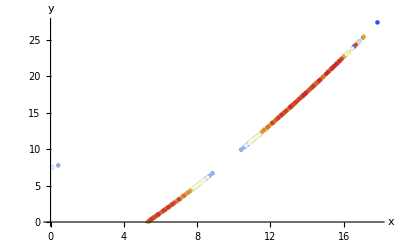

```mathematica
ListPlot[ParallelTable[Style[data1[[t]],ColorData["TemperatureMap"][t/888]],{t,1,888}],PlotRange->All,AxesLabel->{x,y},PlotStyle->PointSize[Medium]]
```

## El péndulo acoplado

Ahora examinamos, de manera numérica, mapeos de Poincaré del sistema del péndulos doble. El péndulo doble es un sistema cuatro dimensional porque está descrito por los dos ángulos de los péndulos, y los dos momentos angulares de los mismos. Las ecuaciones son:




Debajo vemos el mapeo de Poincaré cuando definimos a la sección como la serie de hiperplanos , es decir, cuando el primer péndulo está completamente horizontal, para ciertos valores de los parámetros. Vemos en este caso que, las intersecciones parecen formar curvas cerradas. En este caso, el movimiento es cuasiperiódico.

```mathematica
datap=Reap[NDSolve[{w'[t]==6*(2*y[t]-3*Cos[w[t]-x[t]]*z[t])/(16-9*Cos[w[t]-x[t]]^2),x'[t]==6*(8*z[t]-3*Cos[w[t]-x[t]]*y[t])/(16-9*Cos[w[t]-x[t]]^2),y'[t]==(-1/2)*(w'[t]*x'[t]*Sin[w[t]-x[t]]+30*Sin[w[t]]),z'[t]==(-1/2)*(-w'[t]*x'[t]*Sin[w[t]-x[t]]+10*Sin[x[t]]),w[0]==Pi/4,x[0]==5*Pi/3,y[0]==-1,z[0]==0,WhenEvent[Mod[w[t],2 π]==0,Sow[{x[t],y[t],z[t]}]]},{},{t,0,100000},MaxSteps->∞]][[-1,1]];
```

```mathematica
ListPointPlot3D[datap]
```

-Graphics3D-

```mathematica
datap2=Reap[NDSolve[{w'[t]==6*(2*y[t]-3*Cos[w[t]-x[t]]*z[t])/(16-9*Cos[w[t]-x[t]]^2),x'[t]==6*(8*z[t]-3*Cos[w[t]-x[t]]*y[t])/(16-9*Cos[w[t]-x[t]]^2),y'[t]==(-1/2)*(w'[t]*x'[t]*Sin[w[t]-x[t]]+30*Sin[w[t]]),z'[t]==(-1/2)*(-w'[t]*x'[t]*Sin[w[t]-x[t]]+10*Sin[x[t]]),w[0]==Pi/4,x[0]==5*Pi/3,y[0]==-1,z[0]==0,WhenEvent[Mod[x[t],2 π]==0,Sow[{w[t],y[t],z[t]}]]},{},{t,0,100000},MaxSteps->∞]][[-1,1]];
ListPointPlot3D[datap2]
```

-Graphics3D-

Ahora vemos el mapeo de a misma sección de Poincaré, pero con otros parámetros. Estas nubes de puntos con una subestructura definida son característicos de los sistemas caóticos.

```mathematica
datapc1=Reap[NDSolve[{w'[t]==6*(2*y[t]-3*Cos[w[t]-x[t]]*z[t])/(16-9*Cos[w[t]-x[t]]^2),x'[t]==6*(8*z[t]-3*Cos[w[t]-x[t]]*y[t])/(16-9*Cos[w[t]-x[t]]^2),y'[t]==(-1/2)*(w'[t]*x'[t]*Sin[w[t]-x[t]]+30*Sin[w[t]]),z'[t]==(-1/2)*(-w'[t]*x'[t]*Sin[w[t]-x[t]]+10*Sin[x[t]]),w[0]==Pi/2,x[0]==Pi/2,y[0]==-1,z[0]==0,WhenEvent[Mod[w[t],2 π]==0,Sow[{x[t],y[t],z[t]}]]},{},{t,0,100000},MaxSteps->∞]][[-1,1]];
ListPointPlot3D[datapc1]
```

-Graphics3D-

```mathematica
datapc2=Reap[NDSolve[{w'[t]==6*(2*y[t]-3*Cos[w[t]-x[t]]*z[t])/(16-9*Cos[w[t]-x[t]]^2),x'[t]==6*(8*z[t]-3*Cos[w[t]-x[t]]*y[t])/(16-9*Cos[w[t]-x[t]]^2),y'[t]==(-1/2)*(w'[t]*x'[t]*Sin[w[t]-x[t]]+30*Sin[w[t]]),z'[t]==(-1/2)*(-w'[t]*x'[t]*Sin[w[t]-x[t]]+10*Sin[x[t]]),w[0]==Pi/2,x[0]==Pi/2,y[0]==-1,z[0]==0,WhenEvent[Mod[x[t],2 π]==0,Sow[{w[t],y[t],z[t]}]]},{},{t,0,100000},MaxSteps->∞]][[-1,1]];
ListPointPlot3D[datapc2,PlotRange->All]
```

-Graphics3D-

## Oscilador de Duffing

Éste es un sistema de dos ecuaciones no homogéneas, por lo que podemos tomar al tiempo como una dimensión extra. Las ecuaciones son


Debajo, vemos las trayectorias módulo  en el tiempo. Es decir, en la parte superior e inferior tenemos la sección de Poincaré definida por :

```mathematica
d=0.15;
g=0.3;
```

```mathematica
sduff=NDSolve[{x'[t]==y[t],y'[t]==g*Cos[t]+x[t]-x[t]^3-d*y[t],x[0]==0,y[0]==0},{x,y,z},{t,0,100000}];
```

```mathematica
ParametricPlot3D[Evaluate[{x[t],y[t],Mod[t,2*Pi]}/.sduff],{t,0,100000},MaxRecursion->10,PlotPoints->100,BoxRatios->{1,1,1},AxesLabel->{x,y,t},ColorFunction->Function[{x,y,z,t},ColorData["TemperatureMap"][t]]]
```

-Graphics3D-

Y aquí el mapeo de Poincaré sobre la sección antes mencionada. El sistema es caótico.

```mathematica
data=Block[{δ=0.15,γ=0.3},Reap[NDSolve[{x''[t]+δ x'[t]-x[t]+x[t]^3==γ Cos[t],x[0]==0,x'[0]==0,WhenEvent[Mod[t,2 π]==0,Sow[{x[t],x'[t]}]]},{},{t,0,100000},MaxSteps->∞]]][[-1,1]];
```

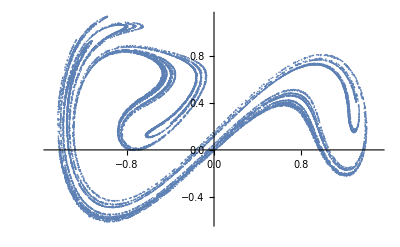

```mathematica
ListPlot[data,PlotRange->{{-1.5,1.5},All}]
```

## Soluciones cuasiperiódicas

Son soluciones que a primera vista, parecen periódicas, pero no logran alcanzar exactamente el mismo valor después de cierto número de oscilaciones.

```mathematica
solpp=NDSolve[{w'[t]==6*(2*y[t]-3*Cos[w[t]-x[t]]*z[t])/(16-9*Cos[w[t]-x[t]]^2),x'[t]==6*(8*z[t]-3*Cos[w[t]-x[t]]*y[t])/(16-9*Cos[w[t]-x[t]]^2),y'[t]==(-1/2)*(w'[t]*x'[t]*Sin[w[t]-x[t]]+30*Sin[w[t]]),z'[t]==(-1/2)*(-w'[t]*x'[t]*Sin[w[t]-x[t]]+10*Sin[x[t]]),w[0]==Pi/4,x[0]==5*Pi/3,y[0]==-1,z[0]==0},{w,x,y,z},{t,0,1000}];
```

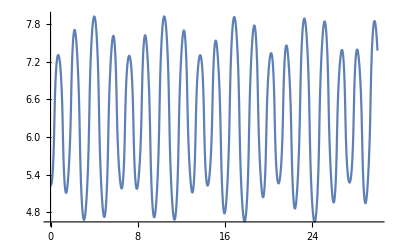

```mathematica
Plot[Evaluate[x[t]/.solpp],{t,0,30}]
```

Aquí vemos una proyección del sistema en dos dimensiones.

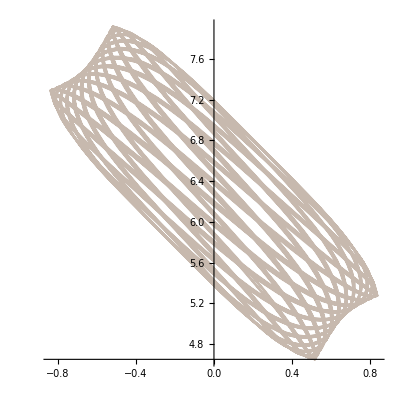

```mathematica
ParametricPlot[Evaluate[{w[t],x[t]}/.solpp],{t,0,100},AspectRatio->1,ColorFunction->Function[{w,x,t},ColorData["TemperatureMap"][t]]]
```

Y aquí una proyección en tres dimensiones. Una característica de la cuasiperiodicidad es el movimiento sobre un toro en tres dimensiones.

```mathematica
Manipulate[ParametricPlot3D[Evaluate[{w[t],x[t],z[t]}/.solpp],{t,0,s},AspectRatio->1,PlotRange->{{-1,1},{4.5,8}},MaxRecursion->10],{s,0.005,36}]
```

Finalmente, vemos sus correspondientes mapeos de Poincaré.

```mathematica
datap=Reap[NDSolve[{w'[t]==6*(2*y[t]-3*Cos[w[t]-x[t]]*z[t])/(16-9*Cos[w[t]-x[t]]^2),x'[t]==6*(8*z[t]-3*Cos[w[t]-x[t]]*y[t])/(16-9*Cos[w[t]-x[t]]^2),y'[t]==(-1/2)*(w'[t]*x'[t]*Sin[w[t]-x[t]]+30*Sin[w[t]]),z'[t]==(-1/2)*(-w'[t]*x'[t]*Sin[w[t]-x[t]]+10*Sin[x[t]]),w[0]==Pi/4,x[0]==5*Pi/3,y[0]==-1,z[0]==0,WhenEvent[Mod[w[t],2 π]==0,Sow[{x[t],y[t],z[t]}]]},{},{t,0,100000},MaxSteps->∞]][[-1,1]];
```

```mathematica
ListPointPlot3D[datap]
```

-Graphics3D-

```mathematica
datap2=Reap[NDSolve[{w'[t]==6*(2*y[t]-3*Cos[w[t]-x[t]]*z[t])/(16-9*Cos[w[t]-x[t]]^2),x'[t]==6*(8*z[t]-3*Cos[w[t]-x[t]]*y[t])/(16-9*Cos[w[t]-x[t]]^2),y'[t]==(-1/2)*(w'[t]*x'[t]*Sin[w[t]-x[t]]+30*Sin[w[t]]),z'[t]==(-1/2)*(-w'[t]*x'[t]*Sin[w[t]-x[t]]+10*Sin[x[t]]),w[0]==Pi/4,x[0]==5*Pi/3,y[0]==-1,z[0]==0,WhenEvent[Mod[x[t],2 π]==0,Sow[{w[t],y[t],z[t]}]]},{},{t,0,100000},MaxSteps->∞]][[-1,1]];
```

```mathematica
ListPointPlot3D[datap2]
```

-Graphics3D-